# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["/Users/pcs/Desktop/Entropy/Calculations/T1 positive parity/T1 FINAL/QMB_offline.wl"];
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

```mathematica
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

# T1

```mathematica
L=8;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=1;
h=1;
g=0.5;
H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
La=L/2;
Lb=L-La;
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
```

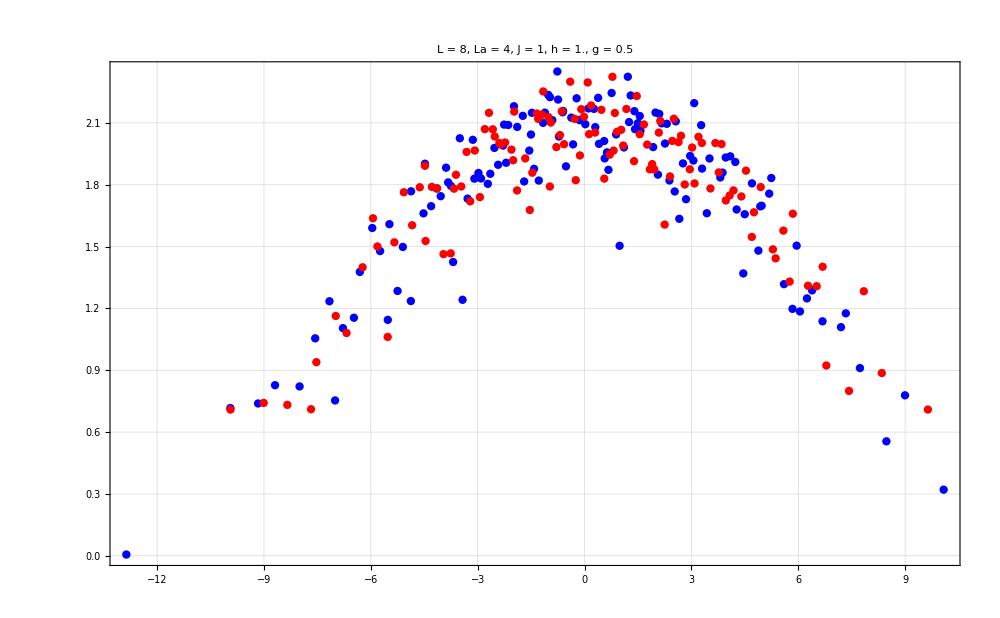

```mathematica
ListPlot[{Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Blue,PointSize[0.006]],Directive[Red,PointSize[0.006]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]]
```

```mathematica
Min[allvals]
Max[allvals]
ΔE=Max[allvals]-Min[allvals]
Δt=1/(4*ΔE)
10^3.5/Δt
```

-9.85419

9.83817

19.6924

0.0126953

249091.

```mathematica
Min[allvals]
Max[allvals]
ΔE=Max[allvals]-Min[allvals]
Δt=1/(4*ΔE)
10^3.5/Δt
```

-12.4095

12.3817

24.7913

0.0100842

313588.

```mathematica
Min[allvals]
Max[allvals]
ΔE=Max[allvals]-Min[allvals]
Δt=1/(4*ΔE)
10^3.5/Δt
```

-14.9689

14.9263

29.8951

0.00836257

378147.

## h

```mathematica
Min[allvals]
Max[allvals]
ΔE=Max[allvals]-Min[allvals]
Δt=1/(4*ΔE)
10^3.5/Δt
```

-15.2397

7.84005

23.0797

0.010832

291938.

```mathematica
Min[allvals]
Max[allvals]
ΔE=Max[allvals]-Min[allvals]
Δt=1/(4*ΔE)
10^3.5/Δt
```

-19.293

9.94042

29.2334

0.00855186

369777.

## Time scale h -> 0

```mathematica
allstates=Table[RandomChainProductState[L],10];
```

```mathematica
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstates=data[[All,2]];
```

```mathematica
tlist=Table[i,{i,0,10^3.5,0.5}];
tlist//Length
```

6325

```mathematica
svntproducta=ParallelTable[{t,svn[L,La,Lb,j,allvals,allvecs,t]},{j,productstates},{t,tlist},DistributedContexts->Full];
```

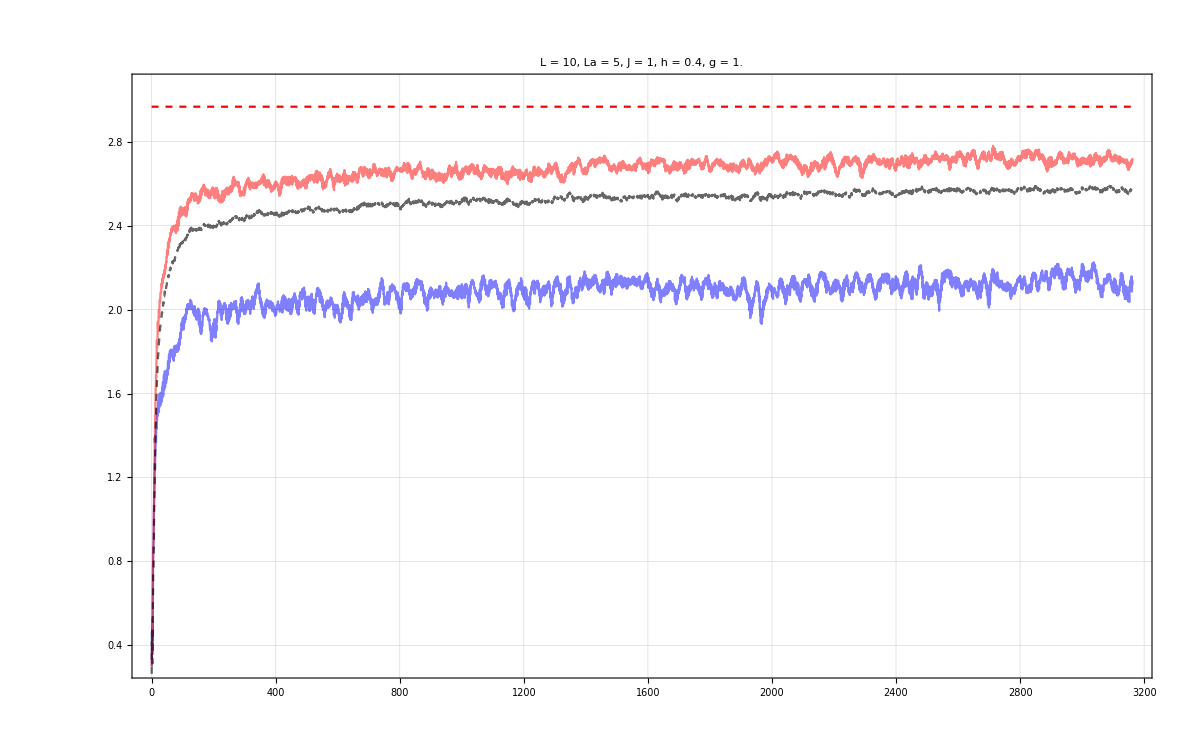

```mathematica
Show[{ListPlot[{svntproducta[[1]],svntproducta[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListPlot[Mean[svntproducta],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

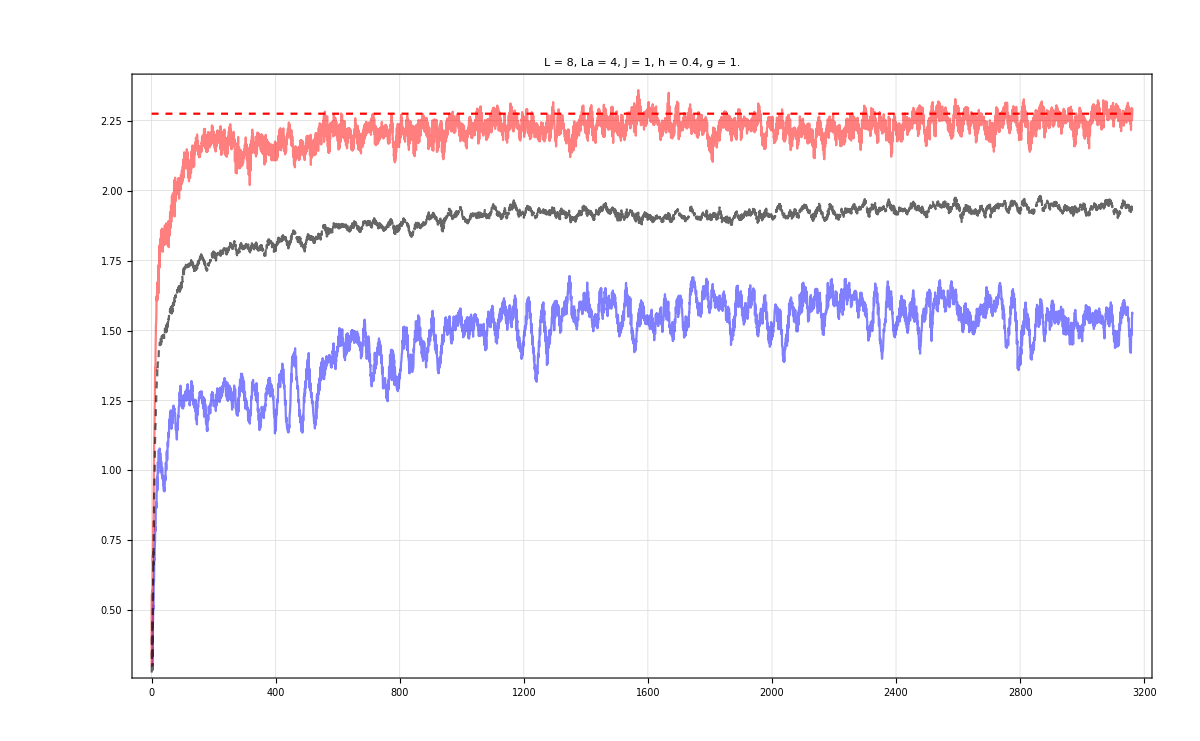

```mathematica
Show[{ListPlot[{svntproducta[[1]],svntproducta[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListPlot[Mean[svntproducta],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

## Time scale g -> 0

```mathematica
allstates=Table[RandomChainProductState[L],5];
```

```mathematica
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstates=data[[All,2]];
```

```mathematica
tlist=Table[i,{i,0,10^3.5,0.5}];
tlist//Length
```

6325

```mathematica
svntproducta=ParallelTable[{t,svn[L,La,Lb,j,allvals,allvecs,t]},{j,productstates},{t,tlist},DistributedContexts->Full];
```

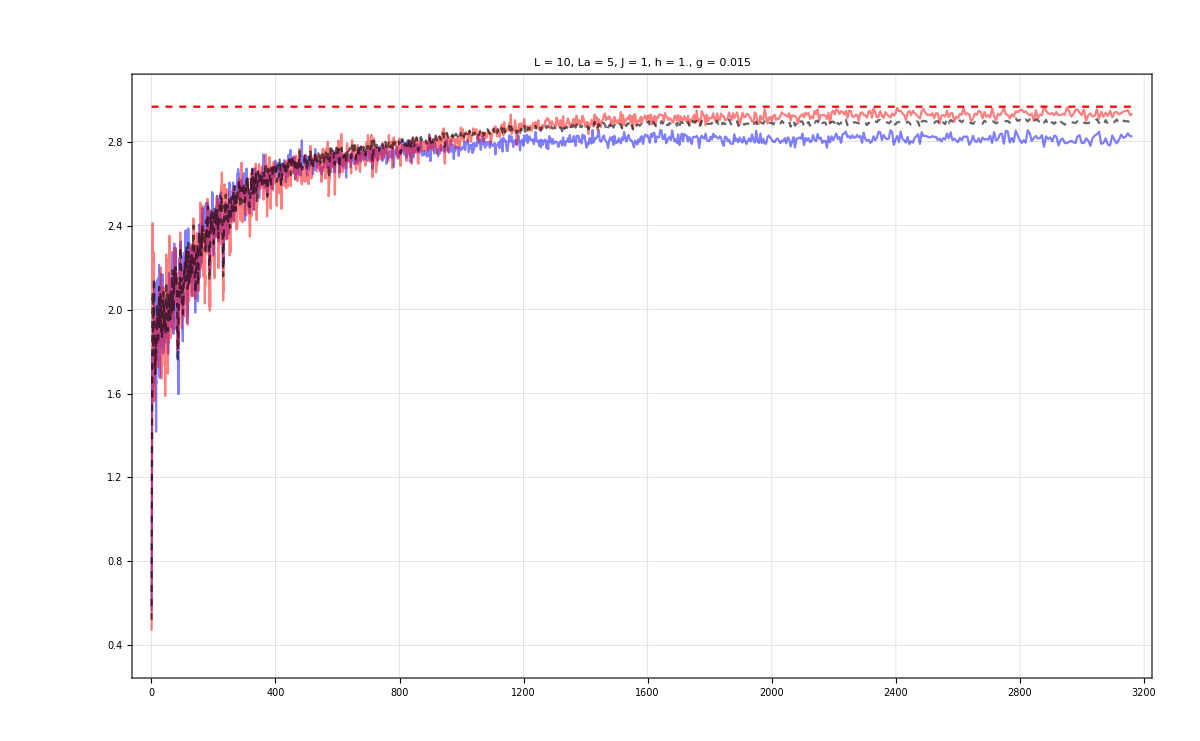

```mathematica
Show[{ListPlot[{svntproducta[[1]],svntproducta[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListPlot[Mean[svntproducta],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

## Examples

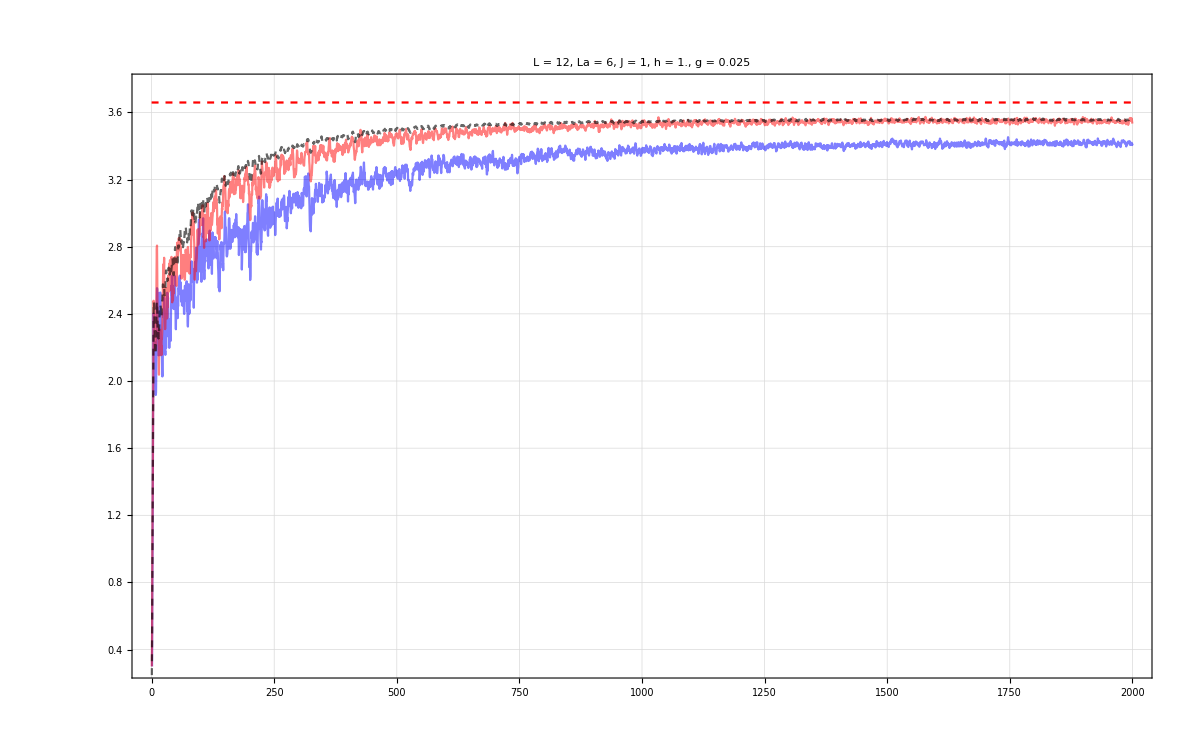

```mathematica
Show[{ListPlot[{svntproducta[[1]],svntproducta[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListPlot[Mean[svntproducta],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

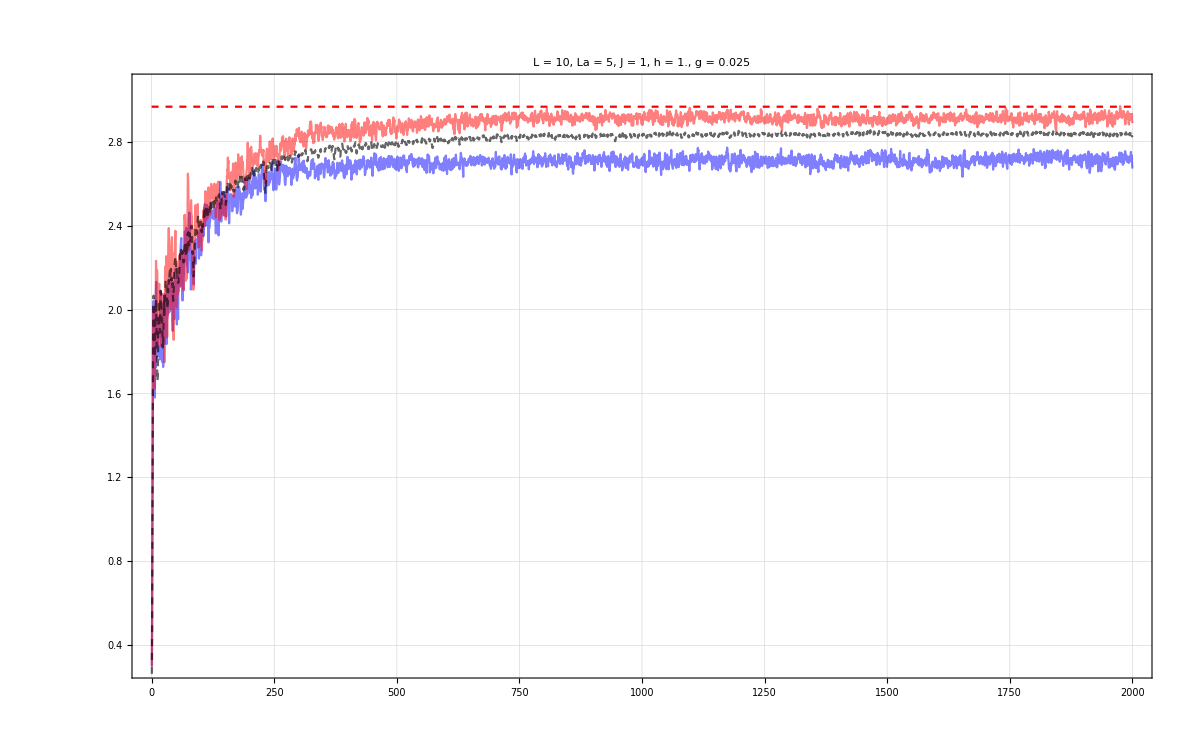

```mathematica
Show[{ListPlot[{svntproducta[[1]],svntproducta[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListPlot[Mean[svntproducta],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

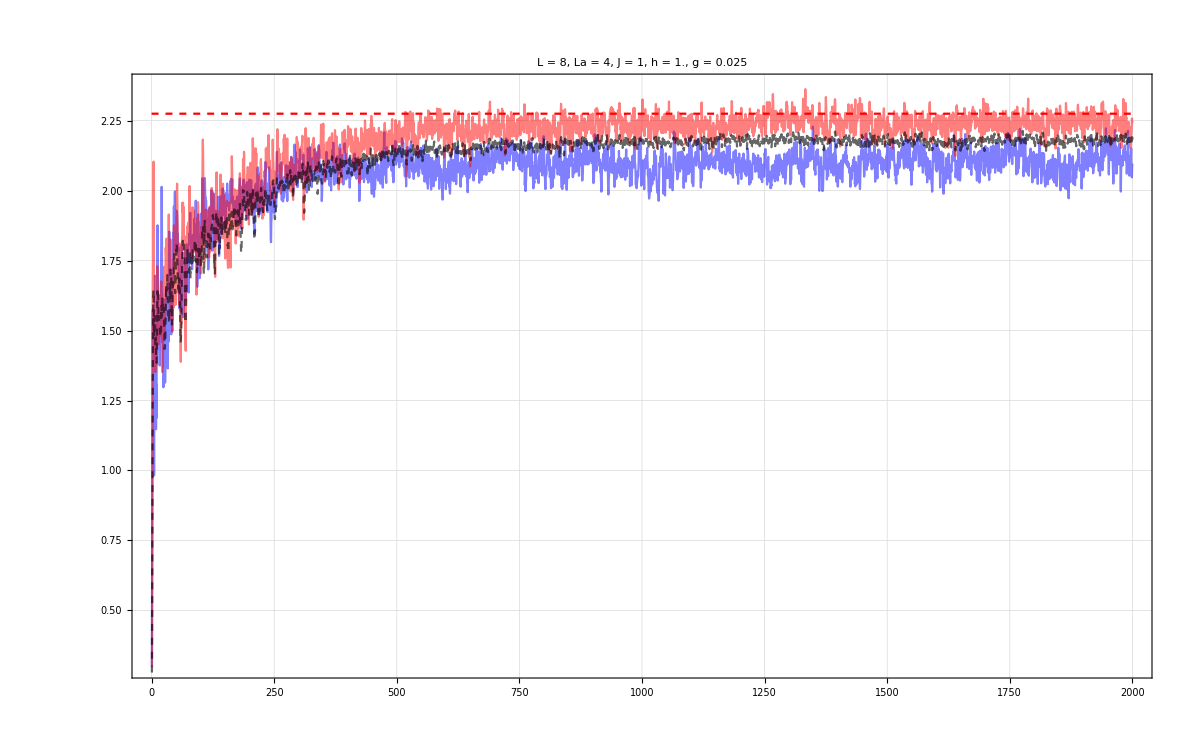

```mathematica
Show[{ListPlot[{svntproducta[[1]],svntproducta[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListPlot[Mean[svntproducta],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

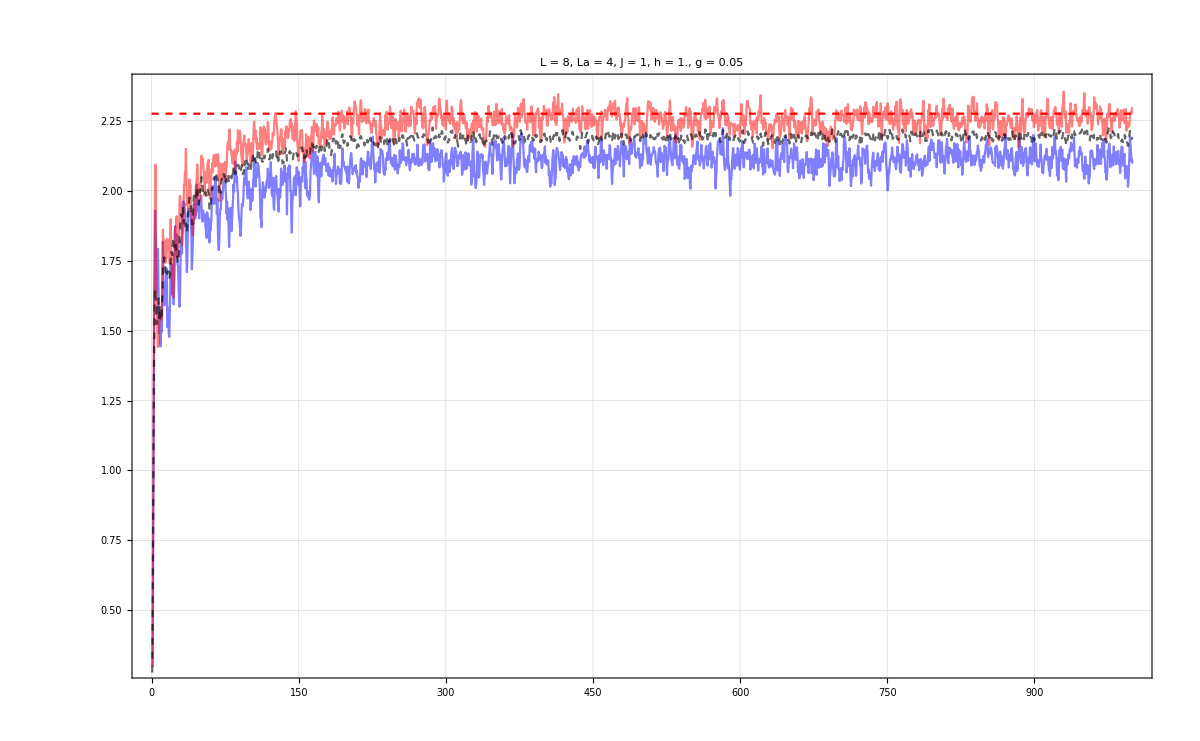

```mathematica
Show[{ListPlot[{svntproducta[[1]],svntproducta[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListPlot[Mean[svntproducta],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

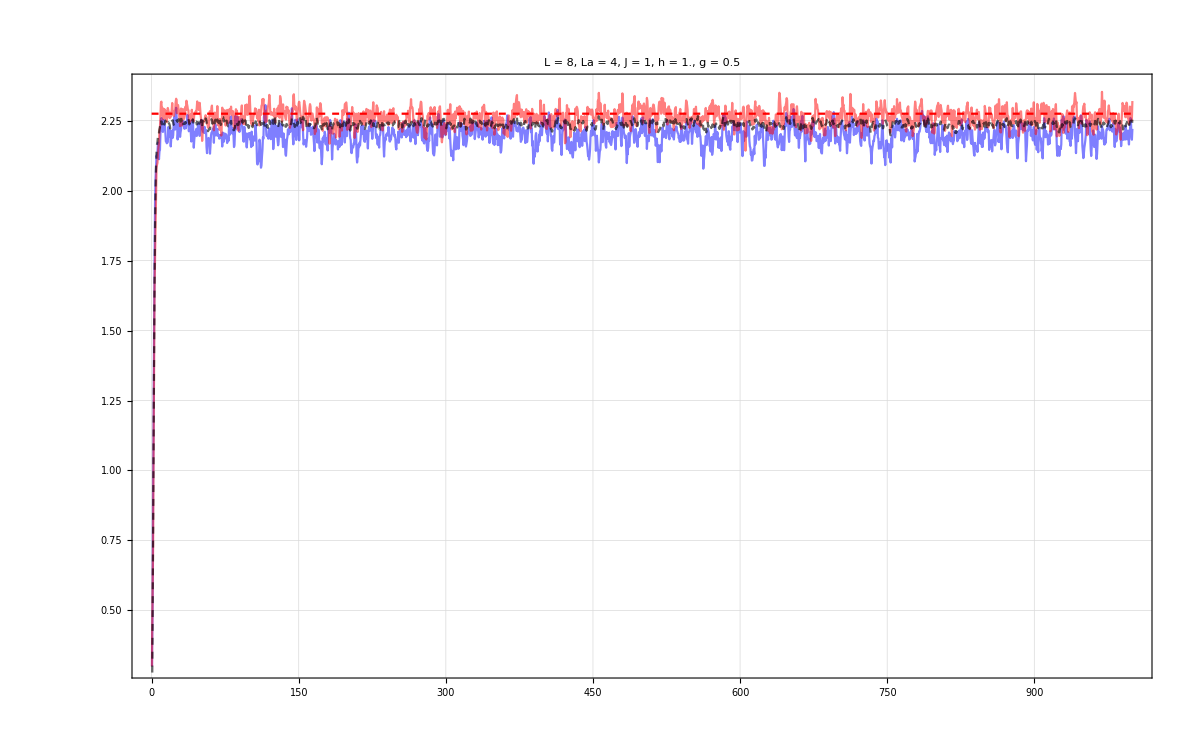

```mathematica
Show[{ListPlot[{svntproducta[[1]],svntproducta[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListPlot[Mean[svntproducta],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

```mathematica
svntproductb=ParallelTable[{t/ΔE,svn[L,La,Lb,j,allvals,allvecs,t]},{j,productstates},{t,tlist},DistributedContexts->Full];
```

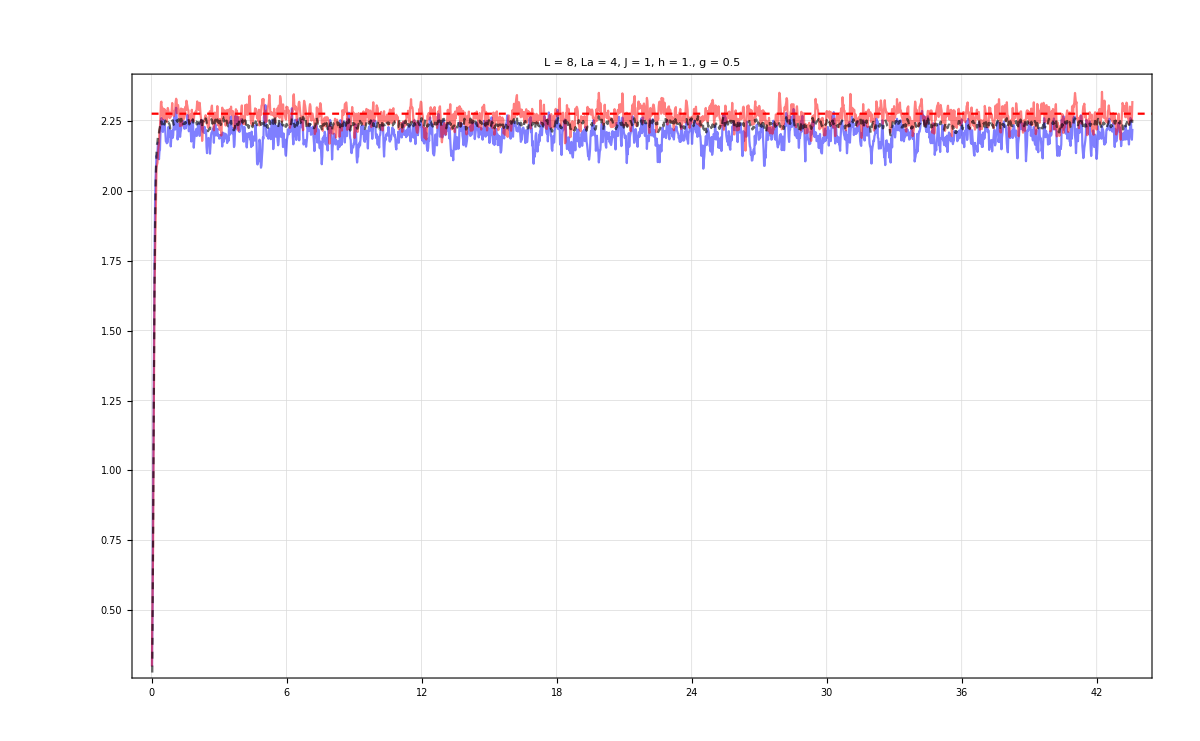

```mathematica
Show[{ListPlot[{svntproductb[[1]],svntproductb[[-1]]},PlotRange->{{tlist[[1]]/ΔE,tlist[[-1]]/ΔE},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListPlot[Mean[svntproductb],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

# RPS

## J=1, h=1, g=0.5, Chaos

```mathematica
allstates={};
Do[
a=Table[RandomQubitState[],L/2];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@a],Flatten[KroneckerProduct@@Reverse[a]]]];
AppendTo[allstates,evenini];
,{i,50}];
```

```mathematica
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstates=data[[All,2]];
```

```mathematica
data[[All,1]]
```

{7.71854,14.2455,14.785,22.3161,25.7166,27.5351,32.9615,34.4994,34.8655,35.0912,35.616,37.113,38.9387,39.1345,39.1396,39.2739,39.4123,41.768,42.5701,43.9466,44.746,46.3471,46.5004,48.0819,50.171,50.6901,50.8985,50.9838,52.7758,52.9191,53.3657,54.0129,55.1137,55.8548,55.9875,56.7888,57.1106,59.0236,60.4741,60.9741,61.3874,62.4022,62.5459,63.9193,64.8233,65.6237,66.0122,67.4676,69.587,69.8296}

```mathematica
tlist=Table[10^i,{i,0,4,0.0020}];
tlist//Length
```

2001

```mathematica
svntproduct=ParallelTable[{t,svn[L,La,Lb,j,allvals,allvecs,t]},{j,productstates},{t,tlist},DistributedContexts->Full];
```

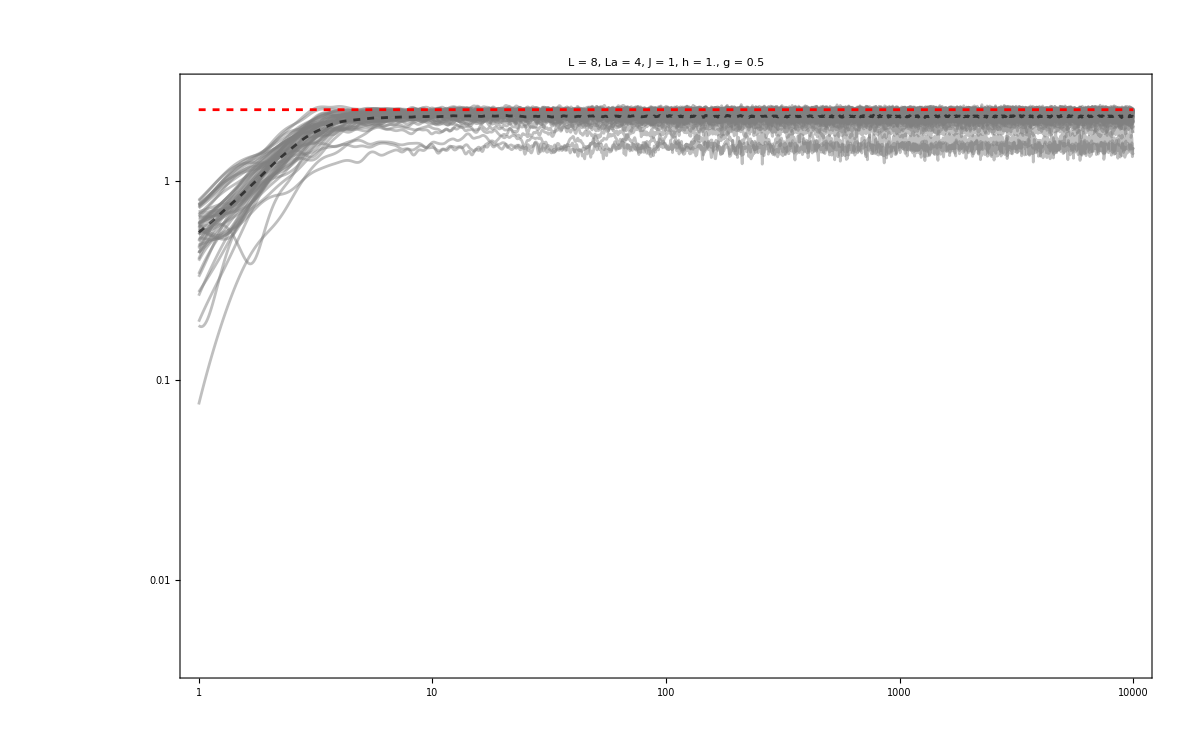

```mathematica
plot2=Show[{ListLogLogPlot[svntproduct,PlotRange->{{tlist[[1]],tlist[[-1]]},{0,3}},Joined->True,PlotStyle->Directive[Gray,Opacity[0.5]],ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["+ RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

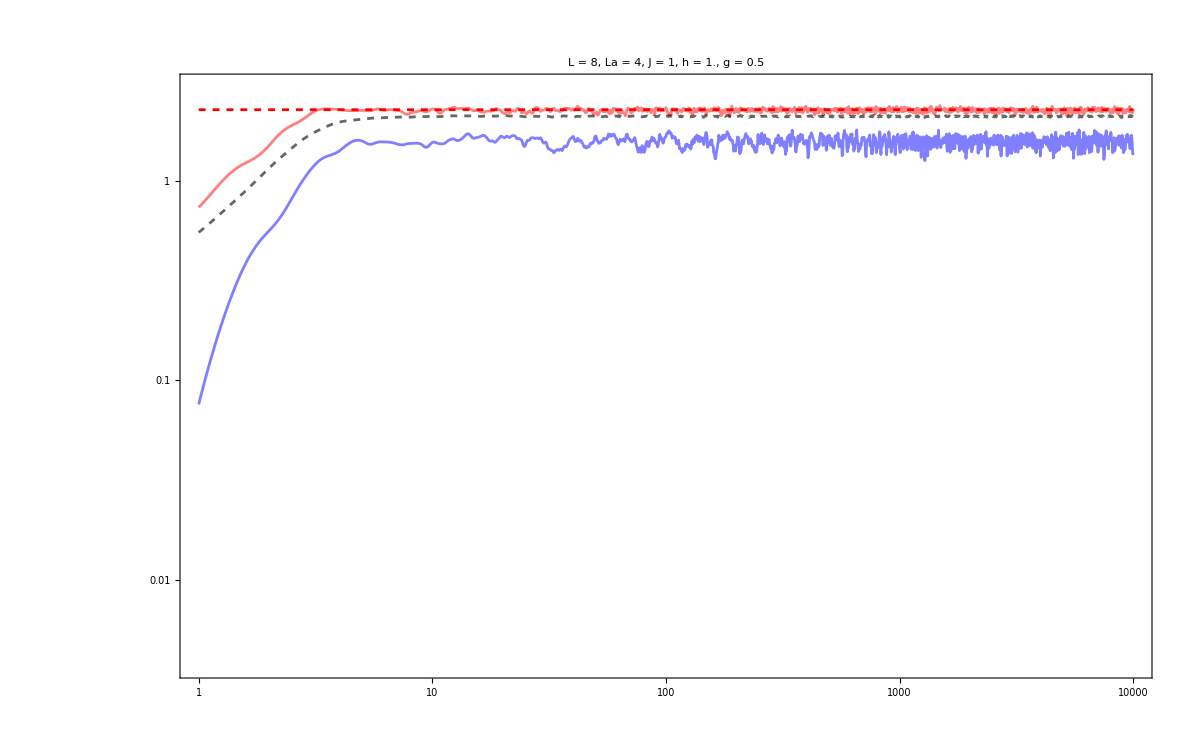

```mathematica
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0,3}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["+ RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

```mathematica
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
Transpose[{data[[All,1]],t1s,limits}]//TableForm
```

7.71854 | 4.50817 | 1.5643
14.2455 | 9.54993 | 1.47329
14.785 | 3.46737 | 1.46212
22.3161 | 3.19154 | 1.77315
25.7166 | 5.67545 | 1.86323
27.5351 | 8.12831 | 2.04315
32.9615 | 3.89045 | 2.00231
34.4994 | 6.45654 | 2.04491
34.8655 | 8.74984 | 2.05765
35.0912 | 6.13762 | 2.04257
35.616 | 8.24138 | 1.94222
37.113 | 11.1173 | 2.02897
38.9387 | 5.97035 | 1.91906
39.1345 | 4.98884 | 2.22313
39.1396 | 3.99945 | 2.08519
39.2739 | 6.95024 | 2.17527
39.4123 | 4.09261 | 2.02501
41.768 | 5.03501 | 2.16557
42.5701 | 6.30957 | 2.1579
43.9466 | 5.97035 | 2.05101
44.746 | 7.11214 | 2.07092
46.3471 | 8.51138 | 2.18681
46.5004 | 6.72977 | 2.1295
48.0819 | 4.80839 | 2.07494
50.171 | 7.11214 | 2.2483
50.6901 | 7.01455 | 2.20779
50.8985 | 5.97035 | 2.22913
50.9838 | 11.6413 | 2.20589
52.7758 | 9.2045 | 2.18146
52.9191 | 4.63447 | 2.17104
53.3657 | 7.4131 | 2.20689
54.0129 | 5.22396 | 2.2266
55.1137 | 10.1391 | 2.1521
55.8548 | 6.91831 | 2.26434
55.9875 | 5.49541 | 2.25969
56.7888 | 10.9144 | 2.19544
57.1106 | 4.42588 | 2.14291
59.0236 | 4.61318 | 2.17562
60.4741 | 6.57658 | 2.23314
60.9741 | 5.39511 | 2.19942
61.3874 | 10.2802 | 2.22836
62.4022 | 6.28058 | 2.25584
62.5459 | 3.68129 | 2.20631
63.9193 | 11.4815 | 2.27032
64.8233 | 3.03389 | 2.25443
65.6237 | 5.70164 | 2.22225
66.0122 | 4.9204 | 2.26912
67.4676 | 6.36796 | 2.22714
69.587 | 8.31764 | 2.25965
69.8296 | 3.20627 | 2.25588

```mathematica
Mean[t1s]
```

6.51111

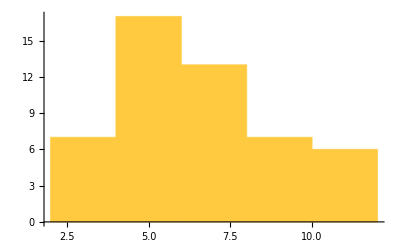

```mathematica
Histogram[t1s]
```

## J=0.1, h=1, g=1, Regular c

```mathematica
allstates={};
Do[
a=Table[RandomQubitState[],L/2];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@a],Flatten[KroneckerProduct@@Reverse[a]]]];
AppendTo[allstates,evenini];
,{i,100}];
```

```mathematica
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstates=data[[All,2]];
```

```mathematica
data[[All,1]]
```

{7.79155,8.17549,10.0984,13.6119,14.5765,14.6825,15.7823,18.1502,18.7032,19.5945,19.8086,20.0263,20.1075,20.5823,21.8621,22.3463,22.8034,22.9595,26.9617,27.4003,27.6122,27.8763,28.1702,29.0279,29.3391,30.2197,30.2497,31.0562,31.0952,31.4834,31.736,32.375,32.5226,32.9146,32.9289,33.0699,33.1979,34.6352,35.1888,35.5069,36.6292,36.6341,36.8973,37.2682,37.6121,37.8178,38.1746,38.831,39.472,39.8848,40.3624,40.5573,41.2012,41.2691,41.3104,41.7656,41.9526,42.7328,43.2336,44.4696,44.6968,45.55,45.5539,45.5753,45.9701,46.93,46.9657,47.4728,47.862,47.977,48.8069,49.407,49.5769,49.6795,50.7888,51.3356,51.8492,53.5191,54.1785,55.0885,55.182,55.2053,55.362,56.2864,57.05,57.073,58.451,59.8562,60.2824,60.9211,61.0751,61.406,61.8033,63.3442,63.624,63.7661,64.574,64.8921,70.8293,75.9958}

```mathematica
tlist=Table[10^i,{i,0,4,0.0010}];
tlist//Length
```

4001

```mathematica
svntproduct=ParallelTable[{t,svn[L,La,Lb,j,allvals,allvecs,t]},{j,productstates},{t,tlist},DistributedContexts->Full];
```

```mathematica
plot2=Show[{ListLogLogPlot[svntproduct,PlotRange->{{tlist[[1]],tlist[[-1]]},{0,3}},Joined->True,PlotStyle->Directive[Gray,Opacity[0.5]],ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["+ RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

-Graphics-

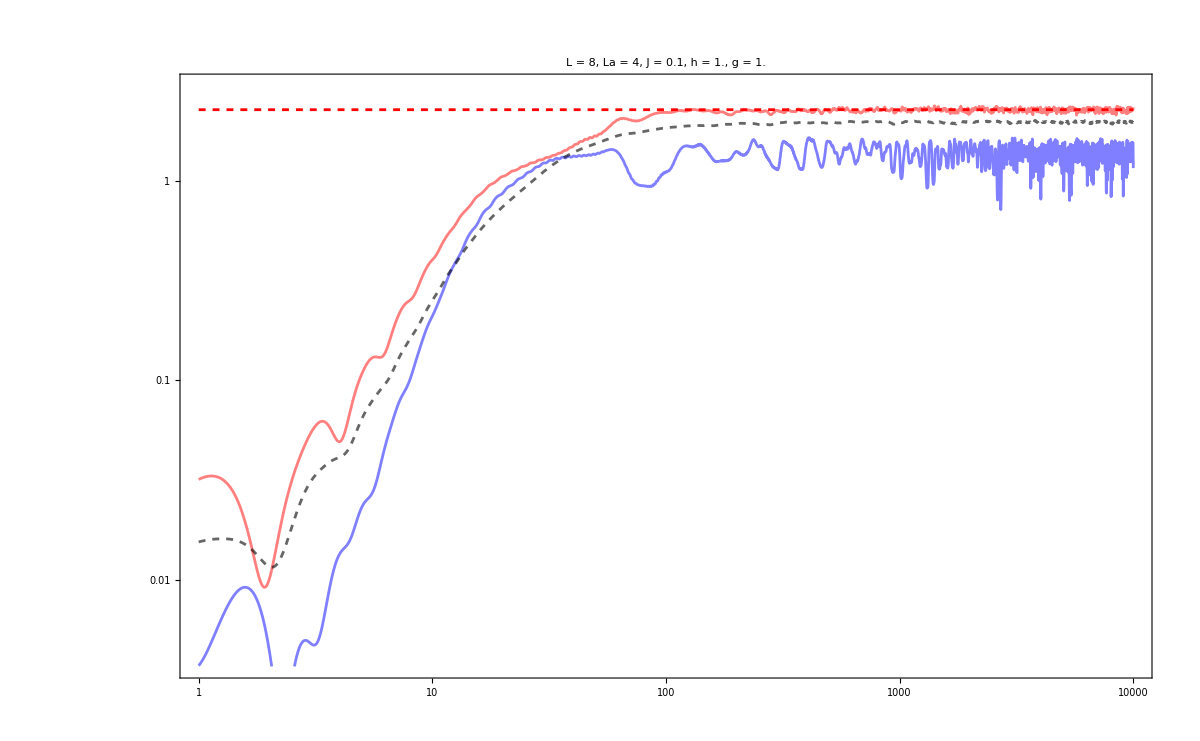

```mathematica
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0,3}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["+ RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

```mathematica
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
Transpose[{data[[All,1]],t1s,limits}]//TableForm
```

7.79155 | 48.3059 | 1.35343
8.17549 | 457.088 | 1.20018
10.0984 | 301.995 | 1.64593
13.6119 | 149.968 | 1.3656
14.5765 | 301.995 | 1.65855
14.6825 | 177.419 | 1.42081
15.7823 | 102.329 | 1.55355
18.1502 | 375.837 | 1.51086
18.7032 | 154.525 | 1.70949
19.5945 | 85.7038 | 1.81525
19.8086 | 118.032 | 1.63193
20.0263 | 176.198 | 1.89112
20.1075 | 331.894 | 1.58754
20.5823 | 110.662 | 1.63071
21.8621 | 75.3356 | 1.63805
22.3463 | 50.8159 | 1.80008
22.8034 | 374.973 | 1.57586
22.9595 | 142.561 | 1.77141
26.9617 | 111.173 | 1.85891
27.4003 | 83.3681 | 1.907
27.6122 | 171.396 | 1.66151
27.8763 | 116.681 | 1.79514
28.1702 | 105.439 | 1.85819
29.0279 | 310.456 | 1.80478
29.3391 | 402.717 | 1.82161
30.2197 | 169.434 | 1.87678
30.2497 | 109.396 | 1.89259
31.0562 | 111.944 | 1.92507
31.0952 | 159.956 | 2.02775
31.4834 | 306.196 | 2.02221
31.736 | 92.8966 | 1.79211
32.375 | 41.115 | 1.91725
32.5226 | 149.968 | 2.06998
32.9146 | 131.22 | 1.90352
32.9289 | 224.388 | 1.94064
33.0699 | 346.737 | 2.0318
33.1979 | 97.949 | 1.98288
34.6352 | 324.34 | 1.92631
35.1888 | 225.944 | 1.85371
35.5069 | 137.088 | 2.05313
36.6292 | 125.314 | 2.00531
36.6341 | 153.109 | 1.9607
36.8973 | 509.331 | 1.90239
37.2682 | 86.4968 | 2.05008
37.6121 | 542.001 | 1.92525
37.8178 | 322.849 | 2.07627
38.1746 | 140.929 | 1.95144
38.831 | 63.5331 | 2.00838
39.472 | 93.9723 | 2.1275
39.8848 | 612.35 | 2.03455
40.3624 | 163.682 | 2.08597
40.5573 | 186.638 | 1.98171
41.2012 | 290.402 | 2.12719
41.2691 | 113.763 | 2.05644
41.3104 | 329.61 | 2.07622
41.7656 | 112.72 | 2.03308
41.9526 | 364.754 | 2.00877
42.7328 | 205.589 | 2.03205
43.2336 | 90.5733 | 2.05019
44.4696 | 99.3116 | 2.04011
44.6968 | 166.725 | 2.08803
45.55 | 96.8278 | 2.14562
45.5539 | 72.277 | 2.1052
45.5753 | 103.514 | 2.13004
45.9701 | 58.3445 | 2.11875
46.93 | 120.504 | 2.13844
46.9657 | 110.662 | 2.09884
47.4728 | 172.982 | 2.11443
47.862 | 113.501 | 2.03651
47.977 | 377.572 | 2.11579
48.8069 | 130.918 | 2.10972
49.407 | 145.211 | 2.07217
49.5769 | 583.445 | 2.09352
49.6795 | 116.145 | 2.13749
50.7888 | 237.137 | 2.15207
51.3356 | 101.158 | 2.09987
51.8492 | 150.314 | 2.06168
53.5191 | 135.831 | 2.09943
54.1785 | 348.337 | 2.12823
55.0885 | 146.218 | 2.14918
55.182 | 206.063 | 2.19266
55.2053 | 134.276 | 2.11332
55.362 | 100.925 | 2.15696
56.2864 | 584.79 | 2.16382
57.05 | 145.881 | 2.13238
57.073 | 89.1251 | 2.12298
58.451 | 113.763 | 2.18978
59.8562 | 127.938 | 2.14152
60.2824 | 187.068 | 2.18048
60.9211 | 192.752 | 2.20979
61.0751 | 90.9913 | 2.18347
61.406 | 126.183 | 2.17357
61.8033 | 153.815 | 2.16178
63.3442 | 133.352 | 2.16548
63.624 | 181.97 | 2.18644
63.7661 | 277.971 | 2.22348
64.574 | 125.314 | 2.19342
64.8921 | 119.124 | 2.16164
70.8293 | 124.165 | 2.21654
75.9958 | 127.644 | 2.26519

```mathematica
Mean[t1s]
```

189.031

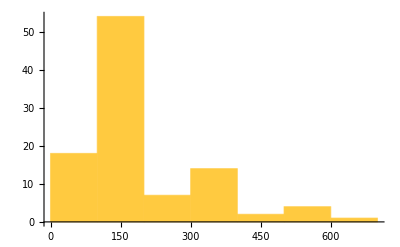

```mathematica
Histogram[t1s]
```

## J=1, h=1, g=0.01, Regular a

```mathematica
allstates={};
Do[
a=Table[RandomQubitState[],L/2];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@a],Flatten[KroneckerProduct@@Reverse[a]]]];
AppendTo[allstates,evenini];
,{i,50}];
```

```mathematica
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstates=data[[All,2]];
```

```mathematica
data[[All,1]]
```

{4.60809,6.65459,8.19692,8.4025,8.63001,8.68867,8.80175,9.63194,9.65336,9.87557,10.0597,10.3548,11.1582,11.1768,11.206,11.8008,11.8606,11.8611,12.2523,12.3639,12.449,12.7015,12.7269,12.8254,13.2905,13.4998,13.6292,13.7779,14.0176,14.0549,14.4113,14.4267,14.5524,14.7631,14.786,14.8966,15.2139,15.7344,15.7971,16.021,16.1504,17.0694,17.1875,17.6027,17.7668,19.3441,20.0124,20.8656,21.1458,21.2843}

```mathematica
tlist=Table[10^i,{i,0,4,0.0010}];
tlist//Length
```

4001

```mathematica
svntproduct=ParallelTable[{t,svn[L,La,Lb,j,allvals,allvecs,t]},{j,productstates},{t,tlist},DistributedContexts->Full];
```

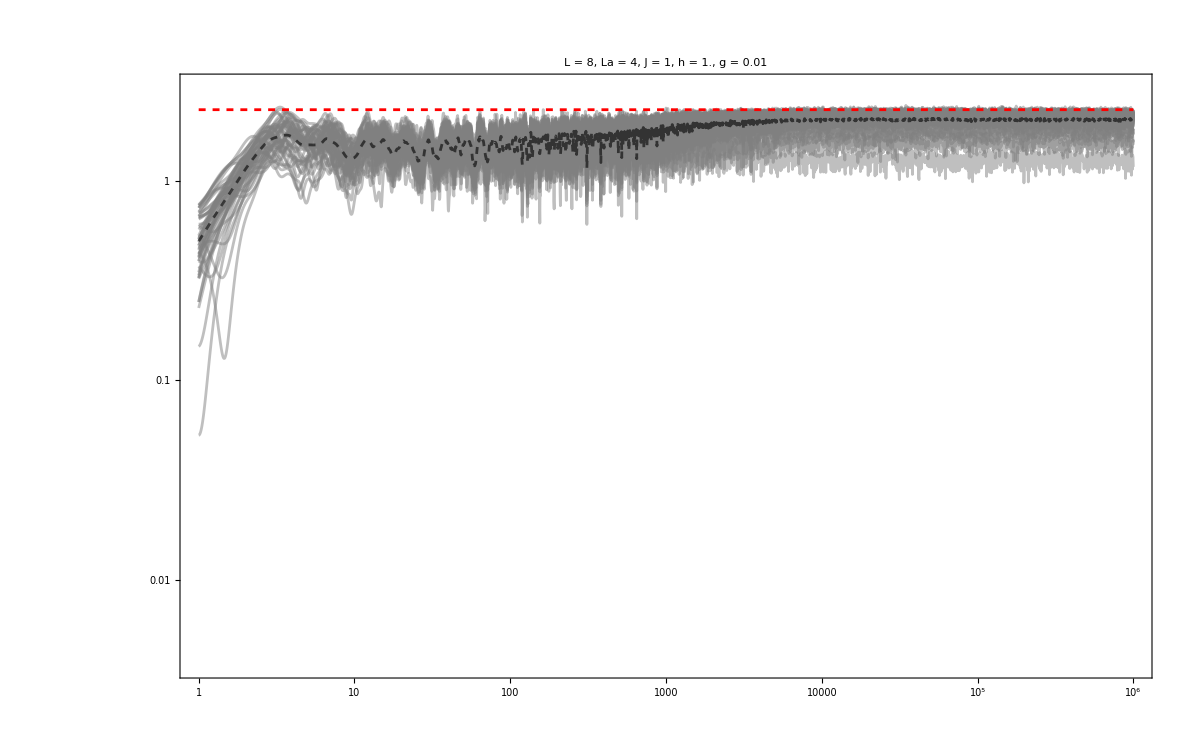

```mathematica
plot2=Show[{ListLogLogPlot[svntproduct,PlotRange->{{tlist[[1]],tlist[[-1]]},{0,3}},Joined->True,PlotStyle->Directive[Gray,Opacity[0.5]],ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["+ RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

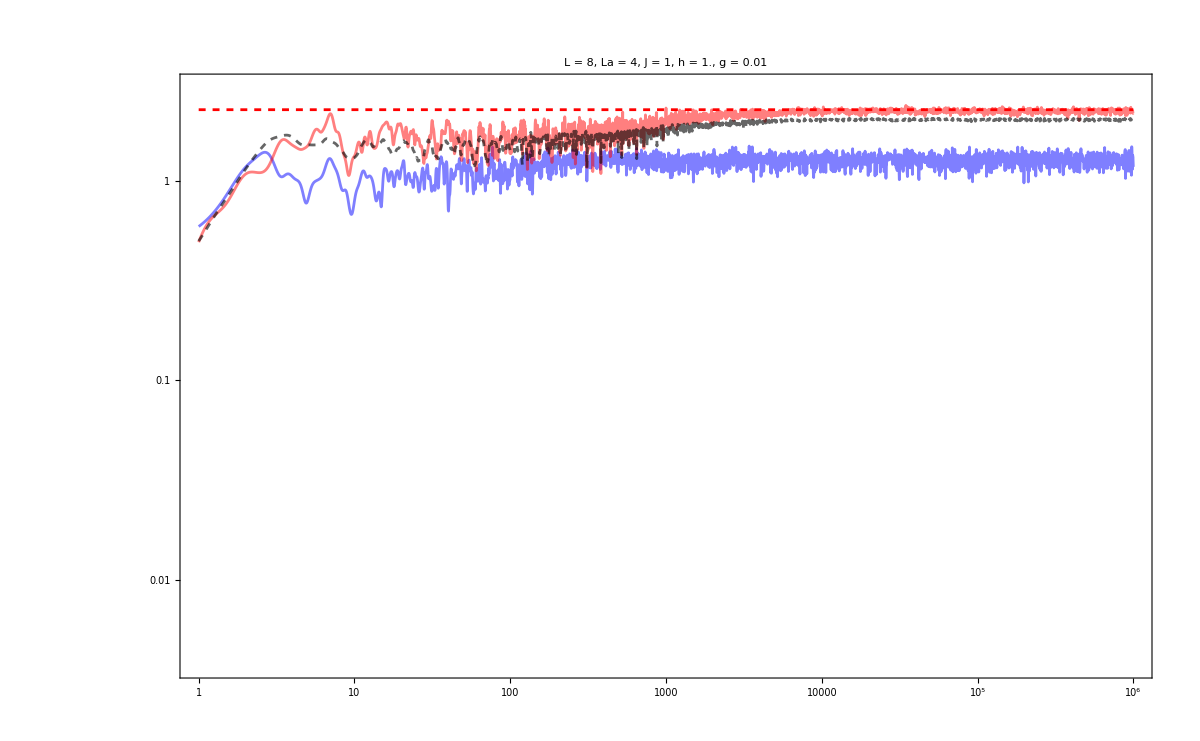

```mathematica
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0,3}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["+ RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

```mathematica
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
Transpose[{data[[All,1]],t1s,limits}]//TableForm
```

9.36279 | 2.22844 | 1.26978
11.0832 | 2.34423 | 1.56217
12.7078 | 2.95121 | 1.51394
17.3942 | 11.4288 | 1.64577
18.5294 | 7.24436 | 1.76755
18.6996 | 64.8634 | 1.81963
21.6928 | 12.1899 | 1.71483
24.8359 | 3.80189 | 2.00265
25.5514 | 46.9894 | 1.80124
26.9032 | 2.71644 | 1.96237
30.7059 | 126.474 | 1.96487
32.587 | 6.54636 | 2.04902
33.403 | 6.54636 | 1.90727
33.8555 | 3.56451 | 1.95487
36.9501 | 79.7995 | 2.02649
37.4509 | 115.878 | 2.01409
38.2918 | 498.884 | 2.03739
38.5431 | 103.753 | 1.99155
38.8146 | 63.6796 | 2.13888
39.3547 | 45.7088 | 2.07977
39.3772 | 376.704 | 2.11415
39.7056 | 2.88403 | 1.99004
40.3432 | 3.11889 | 1.99724
41.2468 | 376.704 | 2.11263
41.5359 | 259.418 | 2.05981
42.759 | 215.774 | 2.08346
43.3028 | 232.274 | 2.06339
43.5772 | 272.898 | 2.06431
44.7721 | 125.314 | 2.15307
45.7383 | 3.56451 | 2.13535
46.0284 | 11.8577 | 2.1264
46.4891 | 303.389 | 2.16742
46.7271 | 1000. | 2.09667
47.9476 | 123.027 | 2.09276
49.3458 | 125.314 | 2.14845
50.4816 | 141.254 | 2.226
51.533 | 1180.32 | 2.1643
51.8533 | 2.92415 | 2.12695
53.6457 | 1096.48 | 2.09887
53.6784 | 12.0226 | 2.19966
54.3242 | 1180.32 | 2.21973
54.8362 | 1111.73 | 2.16038
54.8899 | 744.732 | 2.19214
57.9766 | 714.496 | 2.18041
58.4142 | 162.93 | 2.15887
59.3044 | 498.884 | 2.18811
60.909 | 1914.26 | 2.19367
61.3322 | 1264.74 | 2.17115
63.2329 | 3.13329 | 2.20398
63.5304 | 1000. | 2.23837

```mathematica
Mean[t1s]
```

313.361

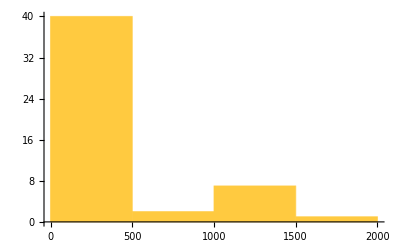

```mathematica
Histogram[t1s]
```

```mathematica
plot2=Show[{ListLogLogPlot[svntproduct,PlotRange->{{tlist[[1]],tlist[[-1]]},{0,3}},Joined->True,PlotStyle->Directive[Gray,Opacity[0.5]],ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["+ RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

-Graphics-

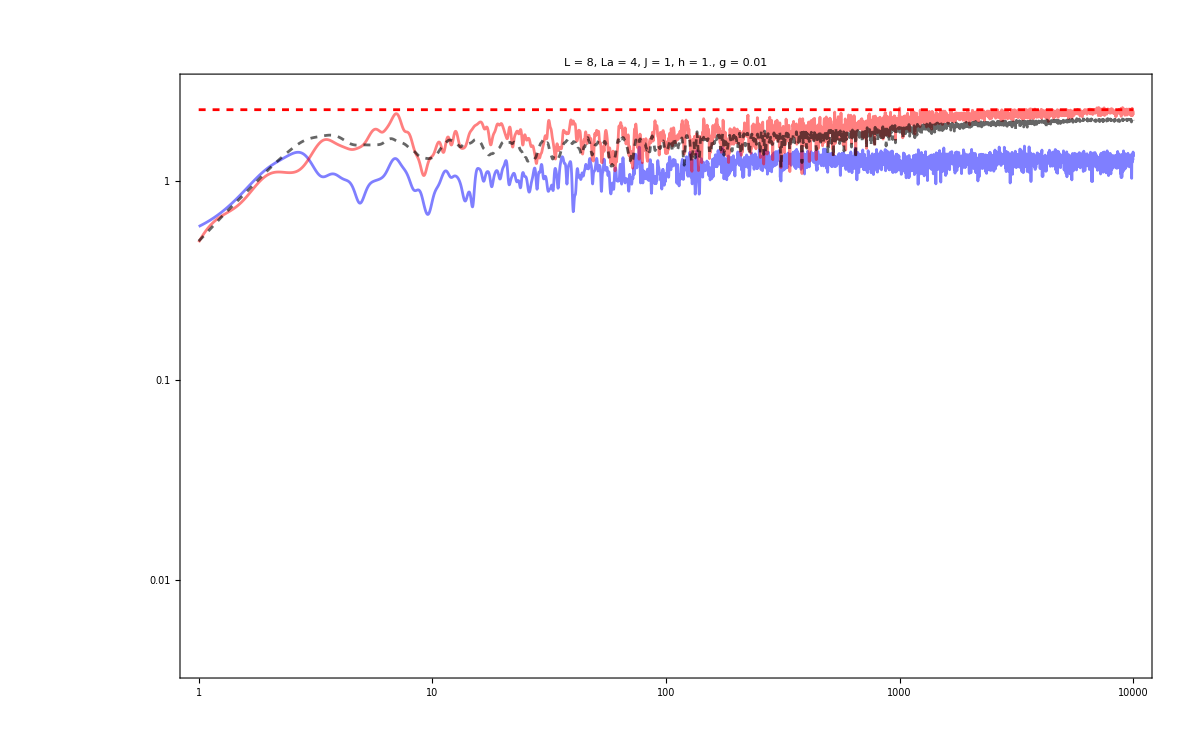

```mathematica
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0,3}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["+ RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

```mathematica
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
Transpose[{data[[All,1]],t1s,limits}]//TableForm
```

9.36279 | 2.1928 | 1.25594
11.0832 | 2.30144 | 1.53393
12.7078 | 2.92415 | 1.5014
17.3942 | 11.3501 | 1.63925
18.5294 | 7.11214 | 1.73564
18.6996 | 64.5654 | 1.81327
21.6928 | 12.1899 | 1.71604
24.8359 | 3.71535 | 1.98179
25.5514 | 46.9894 | 1.805
26.9032 | 2.69774 | 1.94579
30.7059 | 126.474 | 1.97996
32.587 | 6.56145 | 2.06069
33.403 | 6.44169 | 1.88458
33.8555 | 3.52371 | 1.92198
36.9501 | 79.6159 | 2.01266
37.4509 | 115.611 | 1.99963
38.2918 | 498.884 | 2.03819
38.5431 | 103.753 | 1.99675
38.8146 | 63.6796 | 2.14983
39.3547 | 3.83707 | 2.06557
39.3772 | 375.837 | 2.09838
39.7056 | 2.85102 | 1.9657
40.3432 | 3.09742 | 1.9864
41.2468 | 376.704 | 2.12195
41.5359 | 259.418 | 2.03157
42.759 | 215.278 | 2.08985
43.3028 | 6.19441 | 2.04155
43.5772 | 136.144 | 2.05903
44.7721 | 125.026 | 2.13597
45.7383 | 3.53997 | 2.12658
46.0284 | 11.749 | 2.09258
46.4891 | 215.278 | 2.15304
46.7271 | 160.325 | 2.10062
47.9476 | 123.027 | 2.09608
49.3458 | 125.314 | 2.13088
50.4816 | 140.929 | 2.23967
51.533 | 558.47 | 2.13202
51.8533 | 2.92415 | 2.1253
53.6457 | 88.1049 | 2.07309
53.6784 | 3.59749 | 2.17878
54.3242 | 753.356 | 2.22165
54.8362 | 1111.73 | 2.14889
54.8899 | 744.732 | 2.20405
57.9766 | 714.496 | 2.18201
58.4142 | 162.93 | 2.15349
59.3044 | 290.402 | 2.19328
60.909 | 557.186 | 2.17802
61.3322 | 699.842 | 2.14327
63.2329 | 3.11889 | 2.19678
63.5304 | 1000. | 2.22387

```mathematica
Mean[t1s]
```

202.72

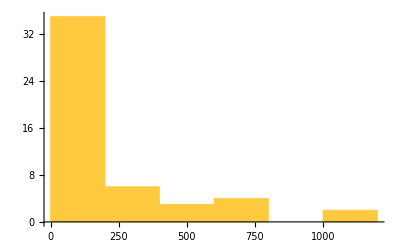

```mathematica
Histogram[t1s]
```

```mathematica
plot2=Show[{ListLogLogPlot[svntproduct,PlotRange->{{tlist[[1]],tlist[[-1]]},{0,3}},Joined->True,PlotStyle->Directive[Gray,Opacity[0.5]],ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["+ RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

-Graphics-

```mathematica
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0,3}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["+ RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

-Graphics-

```mathematica
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
Transpose[{data[[All,1]],t1s,limits}]//TableForm
```

4.60809 | 1.51705 | 0.989802
6.65459 | 2.37137 | 1.15154
8.19692 | 4.89779 | 1.23849
8.4025 | 1.91867 | 1.31214
8.63001 | 2.36592 | 1.2921
8.68867 | 1.86209 | 1.16877
8.80175 | 4.67735 | 1.31801
9.63194 | 2.14289 | 1.1777
9.65336 | 4.69894 | 1.21896
9.87557 | 3.2434 | 1.30951
10.0597 | 1.88365 | 1.19933
10.3548 | 5.4325 | 1.24915
11.1582 | 2.77332 | 1.3784
11.1768 | 1.88799 | 1.20812
11.206 | 2.33346 | 1.30967
11.8008 | 1.99067 | 1.33495
11.8606 | 4.75335 | 1.47704
11.8611 | 4.93174 | 1.41177
12.2523 | 5.17607 | 1.46348
12.3639 | 8.51138 | 1.33334
12.449 | 2.5293 | 1.33041
12.7015 | 4.4157 | 1.31654
12.7269 | 2.73527 | 1.26586
12.8254 | 1.91426 | 1.30021
13.2905 | 2.54683 | 1.49539
13.4998 | 5.49541 | 1.30785
13.6292 | 2.14289 | 1.46856
13.7779 | 8.64968 | 1.39721
14.0176 | 2.01372 | 1.42429
14.0549 | 2.05116 | 1.48514
14.4113 | 23.3346 | 1.41381
14.4267 | 5.87489 | 1.4893
14.5524 | 3.10456 | 1.42545
14.7631 | 2.05116 | 1.3643
14.786 | 4.4157 | 1.41951
14.8966 | 2.03236 | 1.42728
15.2139 | 2.12814 | 1.514
15.7344 | 5.15229 | 1.51981
15.7971 | 2.25424 | 1.44109
16.021 | 2.07014 | 1.56229
16.1504 | 5.22396 | 1.5
17.0694 | 8.45279 | 1.47768
17.1875 | 28.774 | 1.50762
17.6027 | 2.63027 | 1.59322
17.7668 | 17.5792 | 1.52712
19.3441 | 16.8655 | 1.52439
20.0124 | 5.40754 | 1.48878
20.8656 | 46.5586 | 1.51138
21.1458 | 18.239 | 1.55129
21.2843 | 8.47227 | 1.52141

```mathematica
Mean[t1s]
```

6.2897

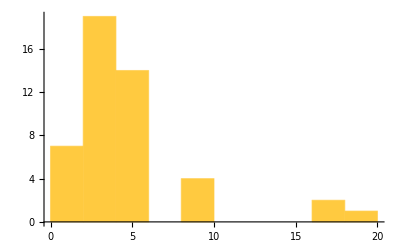

```mathematica
Histogram[t1s]
```

## J=1, h=0.1, g=1, Regular b

```mathematica
allstates={};
Do[
a=Table[RandomQubitState[],L/2];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@a],Flatten[KroneckerProduct@@Reverse[a]]]];
AppendTo[allstates,evenini];
,{i,100}];
```

```mathematica
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstates=data[[All,2]];
```

```mathematica
data[[All,1]]
```

{3.88908,5.3348,6.1588,6.62647,6.81596,7.02342,7.12477,7.83509,8.10201,8.23117,8.71308,8.95548,9.40009,10.5162,10.6916,10.6938,11.0659,12.1472,12.2199,12.9295,12.9837,13.3311,13.6435,13.7446,14.301,14.5542,15.2018,15.6548,15.7073,15.9648,16.4584,16.5855,16.7379,17.548,18.2738,18.4138,18.5688,18.5806,19.3939,20.1523,20.1969,20.8951,21.147,21.2418,22.5574,22.6386,22.6766,22.9679,23.1264,23.7277,23.8918,24.3065,24.3462,24.5724,24.9577,25.18,25.3871,25.5787,26.0013,26.2897,26.3423,27.6998,27.7788,29.2446,29.3229,29.3349,29.5126,29.7703,30.0209,30.2172,30.4822,30.9153,31.268,31.6882,32.137,32.301,32.3288,32.5615,32.718,33.1792,33.2663,35.4718,35.6416,35.8017,36.509,37.9564,38.7513,40.7357,42.7891,43.1491,43.7443,43.9034,46.4117,47.2795,48.5704,51.5019,53.3974,54.7512,57.2441,57.5234}

```mathematica
tlist=Table[10^i,{i,0,4,0.0010}];
tlist//Length
```

4001

```mathematica
svntproduct=ParallelTable[{t,svn[L,La,Lb,j,allvals,allvecs,t]},{j,productstates},{t,tlist},DistributedContexts->Full];
```

```mathematica
plot2=Show[{ListLogLogPlot[svntproduct,PlotRange->{{tlist[[1]],tlist[[-1]]},{0,3}},Joined->True,PlotStyle->Directive[Gray,Opacity[0.5]],ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["+ RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

-Graphics-

```mathematica
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0,3}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["+ RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

-Graphics-

```mathematica
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
Transpose[{data[[All,1]],t1s,limits}]//TableForm
```

3.35115 | 95.4993 | 0.577266
4.37247 | 635.331 | 0.509763
4.79564 | 123.88 | 0.64315
4.94272 | 355.631 | 0.724335
4.95271 | 68.3912 | 0.622262
5.00107 | 1. | 0.456341
5.08977 | 59.9791 | 0.707221
5.28806 | 31.842 | 0.610178
5.30452 | 104.713 | 0.696715
5.38511 | 52.6017 | 0.519094
5.80344 | 62.5173 | 0.740709
6.10919 | 159.221 | 0.547234
6.48972 | 66.3743 | 0.667931
6.85503 | 81.4704 | 0.843111
6.93738 | 109.396 | 0.868182
7.04789 | 127.938 | 0.819858
7.08623 | 389.045 | 0.881321
7.27416 | 657.658 | 0.88122
7.48403 | 387.258 | 0.903014
7.69272 | 106.17 | 0.867428
7.9686 | 417.83 | 0.991446
8.10117 | 1119.44 | 0.905688
8.23507 | 404.576 | 0.977954
8.33264 | 157.761 | 0.755667
8.46919 | 313.329 | 0.79505
8.69712 | 314.775 | 0.8614
8.79545 | 174.985 | 0.679498
8.84577 | 114.025 | 0.989721
9.07413 | 147.231 | 1.0915
9.2693 | 306.902 | 0.813937
9.48492 | 133.968 | 0.848852
9.53451 | 136.458 | 0.884376
10.0156 | 167.494 | 1.06
10.1508 | 145.881 | 1.07497
10.4201 | 87.9023 | 1.00125
10.8392 | 121.899 | 0.944517
11.024 | 108.643 | 0.889064
11.0929 | 115.878 | 0.900158
11.1463 | 1276.44 | 1.07521
11.2862 | 108.143 | 1.00676
11.3042 | 1101.54 | 1.06128
11.4521 | 116.95 | 1.07277
12.4699 | 289.734 | 1.17437
12.5783 | 138.038 | 1.04195
12.8405 | 165.959 | 1.11724
12.9676 | 328.852 | 1.0431
13.9858 | 1205.04 | 1.21581
16.0479 | 133.045 | 1.22767
16.556 | 690.24 | 1.28917
21.4002 | 719.449 | 1.33409

```mathematica
Mean[t1s]
```

288.766

```mathematica
Histogram[t1s]
```

-Graphics-

```mathematica
plot2=Show[{ListLogLogPlot[svntproduct,PlotRange->{{tlist[[1]],tlist[[-1]]},{0,3}},Joined->True,PlotStyle->Directive[Gray,Opacity[0.5]],ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["+ RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

-Graphics-

```mathematica
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0,3}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["+ RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
```

-Graphics-

```mathematica
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
Transpose[{data[[All,1]],t1s,limits}]//TableForm
```

3.88908 | 172.584 | 0.584987
5.3348 | 113.763 | 1.00557
6.1588 | 3265.88 | 0.766745
6.62647 | 415.911 | 0.855934
6.81596 | 504.661 | 1.08412
7.02342 | 1258.93 | 0.946319
7.12477 | 158.125 | 1.00151
7.83509 | 281.838 | 1.11991
8.10201 | 198.153 | 1.18879
8.23117 | 146.555 | 1.17894
8.71308 | 2483.13 | 1.20067
8.95548 | 142.233 | 1.11404
9.40009 | 1905.46 | 0.95696
10.5162 | 5984.12 | 1.33988
10.6916 | 4709.77 | 1.3399
10.6938 | 5370.32 | 1.36723
11.0659 | 484.172 | 1.30836
12.1472 | 638.263 | 1.22799
12.2199 | 2679.17 | 1.29552
12.9295 | 436.516 | 1.28277
12.9837 | 957.194 | 1.30905
13.3311 | 4841.72 | 1.6227
13.6435 | 1096.48 | 1.39685
13.7446 | 5046.61 | 1.60656
14.301 | 857.038 | 1.39813
14.5542 | 2728.98 | 1.51077
15.2018 | 5688.53 | 1.5912
15.6548 | 1412.54 | 1.49693
15.7073 | 4875.28 | 1.32291
15.9648 | 3664.38 | 1.54763
16.4584 | 1648.16 | 1.47879
16.5855 | 1216.19 | 1.4213
16.7379 | 2285.6 | 1.39686
17.548 | 895.365 | 1.40905
18.2738 | 4102.04 | 1.51552
18.4138 | 4295.36 | 1.50256
18.5688 | 1419.06 | 1.226
18.5806 | 794.328 | 1.75145
19.3939 | 3810.66 | 1.48055
20.1523 | 5382.7 | 1.53343
20.1969 | 1629.3 | 1.58371
20.8951 | 4841.72 | 1.76499
21.147 | 868.96 | 1.42527
21.2418 | 827.942 | 1.71181
22.5574 | 2084.49 | 1.71137
22.6386 | 4045.76 | 1.39958
22.6766 | 2792.54 | 1.51068
22.9679 | 5559.04 | 1.75489
23.1264 | 4508.17 | 1.49825
23.7277 | 4207.27 | 1.80242
23.8918 | 3589.22 | 1.53022
24.3065 | 1887.99 | 1.56378
24.3462 | 4508.17 | 1.73746
24.5724 | 1729.82 | 1.97738
24.9577 | 1035.14 | 1.60002
25.18 | 1218.99 | 1.70665
25.3871 | 308.319 | 1.65831
25.5787 | 1729.82 | 1.6714
26.0013 | 2018.37 | 1.73448
26.2897 | 4036.45 | 1.76847
26.3423 | 3837.07 | 1.72274
27.6998 | 1651.96 | 1.79563
27.7788 | 1931.97 | 1.80263
29.2446 | 1503.14 | 1.66474
29.3229 | 1849.27 | 1.5834
29.3349 | 957.194 | 1.73628
29.5126 | 3499.45 | 1.76377
29.7703 | 1698.24 | 1.71188
30.0209 | 3749.73 | 1.79527
30.2172 | 2238.72 | 1.70835
30.4822 | 4508.17 | 1.84899
30.9153 | 4841.72 | 1.63651
31.268 | 3639.15 | 1.84651
31.6882 | 2046.44 | 1.64373
32.137 | 3664.38 | 1.89859
32.301 | 4092.61 | 1.83606
32.3288 | 3715.35 | 1.45541
32.5615 | 4886.52 | 1.73484
32.718 | 1499.68 | 1.72184
33.1792 | 1448.77 | 1.82335
33.2663 | 944.061 | 1.73502
35.4718 | 2360.48 | 1.84649
35.6416 | 3810.66 | 1.79002
35.8017 | 2009.09 | 1.8367
36.509 | 3467.37 | 1.83849
37.9564 | 4265.8 | 1.92709
38.7513 | 2786.12 | 1.77268
40.7357 | 2857.59 | 1.82493
42.7891 | 3061.96 | 1.95956
43.1491 | 4875.28 | 1.97418
43.7443 | 1570.36 | 1.94151
43.9034 | 1428.89 | 1.91489
46.4117 | 4497.8 | 1.85397
47.2795 | 2333.46 | 1.80841
48.5704 | 3523.71 | 1.92349
51.5019 | 4265.8 | 2.00377
53.3974 | 4613.18 | 2.08672
54.7512 | 3723.92 | 2.02572
57.2441 | 2971.67 | 1.96189
57.5234 | 2978.52 | 2.02197

```mathematica
Mean[t1s]
```

2614.

```mathematica
Histogram[t1s]
```

-Graphics-

```mathematica
t1s[[-10;;-1]]
```

{1570.36,1428.89,4497.8,2333.46,3523.71,4265.8,4613.18,3723.92,2971.67,2978.52}

# Full RPS

## h

```mathematica
allstates=Table[RandomChainProductState[L],20];
```

```mathematica
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstates=data[[All,2]];
```

```mathematica
(*Δt=1/((4)(Max[allvals]-Min[allvals]));
tlist=Table[i,{i,0,10^3,Δt}];
tlist//Length*)
```

```mathematica
tlist=Table[10^i,{i,0,3,0.005}];
tlist//Length
```

601

```mathematica
svntproduct=ParallelTable[{t,svn[L,La,Lb,j,allvals,allvecs,t]},{j,productstates},{t,tlist},DistributedContexts->Full];
```

```mathematica
Show[{ListLogLogPlot[svntproduct,PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Gray,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  E",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  PR",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black]]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black]]
```

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

```mathematica
Show[{ListLogLogPlot[svntproduct,PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Gray,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  E",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  PR",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black]]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black]]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

```mathematica
Show[{ListLogLogPlot[svntproduct,PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Gray,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  E",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  PR",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black]]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black]]
```

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

```mathematica
Show[{ListLogLogPlot[svntproduct,PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Gray,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  E",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  PR",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black]]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black]]
```

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

```mathematica
Show[{ListLogLogPlot[svntproduct,PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Gray,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  E",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  PR",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black]]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black]]
```

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

```mathematica
Show[{ListLogLogPlot[svntproduct,PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Gray,Opacity[0.1]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  E",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  PR",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black]]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black]]
```

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

## Examples

```mathematica
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  E",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  PR",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black]]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black]]
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

```mathematica
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  E",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  PR",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black]]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black]]
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

## g

```mathematica
(*allstates={};
Do[
a=Table[RandomQubitState[],L/2];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@a],Flatten[KroneckerProduct@@Reverse[a]]]];
AppendTo[allstates,evenini];
,{i,100}];*)
```

```mathematica
(*allstates=Table[RandomChainProductState[L],1000];*)
```

```mathematica
(*iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstates=data[[All,2]];*)
```

```mathematica
(*Δt=1/((4)(Max[allvals]-Min[allvals]));
tlist=Table[i,{i,0,10^3,Δt}];
tlist//Length*)
```

```mathematica
tlist=Table[10^i,{i,0,3.5,0.0010}];
tlist//Length
```

3501

```mathematica
svntproduct=ParallelTable[{t,svn[L,La,Lb,j,allvals,allvecs,t]},{j,productstates},{t,tlist},DistributedContexts->Full];
```

$Aborted

```mathematica
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  E",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  PR",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black]]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black]]
```

```mathematica
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  E",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  PR",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black]]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black]]
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

## Examples L=8

```mathematica
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,1.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)/PageV  vs  E",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)/PageV  vs  PR",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black]]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)/PageV",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black]]
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

```mathematica
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,1.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)/PageV  vs  E",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)/PageV  vs  PR",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black]]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)/PageV",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black]]
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

```mathematica
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,1.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)/PageV  vs  E",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)/PageV  vs  PR",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black]]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)/PageV",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black]]
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

```mathematica
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,1.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)/PageV  vs  E",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)/PageV  vs  PR",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black]]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)/PageV",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black]]
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

```mathematica
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,1.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)/PageV  vs  E",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)/PageV  vs  PR",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black]]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)/PageV",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black]]
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

```mathematica
(*plot2=Show[{ListLogLogPlot[svntproduct,PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,1.1}},Joined->True,PlotStyle->Directive[Gray,Opacity[0.08]],ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]*)
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,1.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)/PageV  vs  E",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)/PageV  vs  PR",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black]]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)/PageV",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black]]
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

```mathematica
(*plot2=Show[{ListLogLogPlot[svntproduct,PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,1.1}},Joined->True,PlotStyle->Directive[Gray,Opacity[0.08]],ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]*)
Show[{ListLogLogPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,1.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->1200,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListLogLogPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],LogLogPlot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
info=list[[All,2]];
limit=Mean[info[[-200;;-1]]];
position=FirstPosition[info-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)/PageV  vs  E",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)/PageV  vs  PR",20,Black]]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black]]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)/PageV",20,Black]]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black]]
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

# Completely chaotic

```mathematica
ListPlot[{Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Blue,PointSize[0.006]],Directive[Red,PointSize[0.006]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]]
```

-Graphics-

```mathematica
allstates=Table[RandomChainProductState[L],2000];
```

```mathematica
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstates=data[[All,2]];
```

```mathematica
(*Δt=1/((4)(Max[allvals]-Min[allvals]));
tlist=Table[i,{i,0,10^3,Δt}];
tlist//Length*)
```

```mathematica
tlist=Table[i,{i,0,30,0.01}];
tlist//Length
```

3001

```mathematica
svntproduct=ParallelTable[{t,svn[L,La,Lb,j,allvals,allvecs,t]},{j,productstates},{t,tlist},DistributedContexts->Full];
```

```mathematica
Show[{ListPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
series=list[[All,2]];
limit=Mean[series[[-100;;-1]]];
position=FirstPosition[series-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
unsortedlimits=info[[All,3]];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black],ImageSize->700]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  E",20,Black],ImageSize->700]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  PR",20,Black],ImageSize->700]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black],ImageSize->700]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)",20,Black],ImageSize->700]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black],ImageSize->700]
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

```mathematica
ListPlot[Transpose[{Log[info[[All,1]]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  Log(PR)",20,Black],ImageSize->900]
```

-Graphics-

```mathematica
ListPlot[Transpose[{Log[info[[All,1]]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs Log(PR)",20,Black],ImageSize->700]
```

-Graphics-

```mathematica
infostates=SortBy[Transpose[{t1s,energies,sortediprs,limits,productstates}],First];
productstates=infostates[[All,5]];
sortedenergies=infostates[[All,2]];
sortediprs=infostates[[All,3]];
sortedt1s=infostates[[All,1]];
sortedlimits=infostates[[All,4]];
```

```mathematica
ope2=H.H;
variance=ParallelTable[Sqrt[Chop[Conjugate[i].ope2.i]-Chop[Conjugate[i].H.i]^2],{i,productstates},DistributedContexts->Full];
```

```mathematica
ListPlot[sortedt1s,PlotRange->All]
ListPlot[sortediprs,PlotRange->All]
ListPlot[sortedlimits,PlotRange->All]
ListPlot[energies,PlotRange->All]
ListPlot[variance,PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

## L = 10

```mathematica
Show[{ListPlot[{svntproduct[[1]],svntproduct[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproduct[[j]];
times=tlist;
series=list[[All,2]];
limit=Mean[series[[-200;;-1]]];
position=FirstPosition[series-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstates]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstates},DistributedContexts->Full];
info=Transpose[{sortediprs,t1s,limits,energies}];
unsortedlimits=info[[All,3]];
ListPlot[Transpose[{info[[All,4]],Log[info[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Ln(PR) vs E",20,Black],ImageSize->900]
ListPlot[Transpose[{info[[All,4]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  E",20,Black],ImageSize->900]
ListPlot[Transpose[{info[[All,1]],info[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["S(∞)  vs  PR",20,Black],ImageSize->900]
ListPlot[Transpose[{info[[All,1]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs PR",20,Black],ImageSize->900]
ListPlot[Transpose[{info[[All,3]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs S(∞)",20,Black],ImageSize->900]
ListPlot[Transpose[{info[[All,4]],info[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["T1 vs E",20,Black],ImageSize->900]
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

```mathematica
infostates=SortBy[Transpose[{t1s,energies,sortediprs,limits,productstates}],First];
productstates=infostates[[All,5]];
sortedenergies=infostates[[All,2]];
sortediprs=infostates[[All,3]];
sortedt1s=infostates[[All,1]];
```

```mathematica
q=1;
ListPlot[Transpose[{allvals,Abs[Conjugate[allvecs].productstates[[q]]]^2}],PlotRange->All,Filling->Bottom,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["E = "<>ToString[N[sortedenergies[[q]]]]<>", PR = "<>ToString[N[sortediprs[[q]]]]<>", T1 = "<>ToString[N[sortedt1s[[q]]]],25,Black]]
q=50;
ListPlot[Transpose[{allvals,Abs[Conjugate[allvecs].productstates[[q]]]^2}],PlotRange->All,Filling->Bottom,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["E = "<>ToString[N[sortedenergies[[q]]]]<>", PR = "<>ToString[N[sortediprs[[q]]]]<>", T1 = "<>ToString[N[sortedt1s[[q]]]],25,Black]]
q=-1;
ListPlot[Transpose[{allvals,Abs[Conjugate[allvecs].productstates[[q]]]^2}],PlotRange->All,Filling->Bottom,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["E = "<>ToString[N[sortedenergies[[q]]]]<>", PR = "<>ToString[N[sortediprs[[q]]]]<>", T1 = "<>ToString[N[sortedt1s[[q]]]],25,Black]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Histogram[allvals,50]
```

-Graphics-

```mathematica
plots=Table[ListPlot[Transpose[{allvals,Abs[Conjugate[allvecs].productstates[[q]]]^2}],PlotRange->All,Filling->Bottom,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["E = "<>ToString[N[sortedenergies[[q]]]]<>", PR = "<>ToString[N[sortediprs[[q]]]]<>", T1 = "<>ToString[N[sortedt1s[[q]]]],25,Black]],{q,1,Length[productstates],25}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

```mathematica
plots2=Table[Show[{ListPlot[svntproduct[[q]],PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black]],ListPlot[Mean[svntproduct],PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{unsortedlimits[[q]],pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed],Directive[Orange,Dashed]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}}]}],{q,1,Length[productstates],25}];
```

```mathematica
ListAnimate[plots2,AnimationRunning->False]
```